```mathematica
Subsets[EdgeList[GraphComplement[CycleGraph[5]]]]
```

{{},{1<->3},{1<->4},{2<->4},{2<->5},{3<->5},{1<->3,1<->4},{1<->3,2<->4},{1<->3,2<->5},{1<->3,3<->5},{1<->4,2<->4},{1<->4,2<->5},{1<->4,3<->5},{2<->4,2<->5},{2<->4,3<->5},{2<->5,3<->5},{1<->3,1<->4,2<->4},{1<->3,1<->4,2<->5},{1<->3,1<->4,3<->5},{1<->3,2<->4,2<->5},{1<->3,2<->4,3<->5},{1<->3,2<->5,3<->5},{1<->4,2<->4,2<->5},{1<->4,2<->4,3<->5},{1<->4,2<->5,3<->5},{2<->4,2<->5,3<->5},{1<->3,1<->4,2<->4,2<->5},{1<->3,1<->4,2<->4,3<->5},{1<->3,1<->4,2<->5,3<->5},{1<->3,2<->4,2<->5,3<->5},{1<->4,2<->4,2<->5,3<->5},{1<->3,1<->4,2<->4,2<->5,3<->5}}

```mathematica
Graph[
```

```mathematica
Table[
With[
{g=EdgeAdd[CycleGraph[5],edges]},
ColorMainMatrix[g,Graph[#,VertexLabels->"Name",PlotLabel->{edges,ChromaticPolynomial[#,4]/24},ImageSize->120]&]
]
,{edges,Subsets[EdgeList[GraphComplement[CycleGraph[5]]]]}]
```

{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 10
0 | 0
10 | 3
7 | 3
7 | 0
10
2 |  | 10
0 | 0
10 | 3
7 | 3
7
3 |  |  | 10
0 | 0
10 | 3
7
4 |  |  |  | 10
0 | 0
10
5 |  |  |  |  | 10
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
0 | 0
7 | 0
7 | 3
4 | 0
7
2 |  | 7
0 | 0
7 | 2
5 | 2
5
3 |  |  | 7
0 | 0
7 | 3
4
4 |  |  |  | 7
0 | 0
7
5 |  |  |  |  | 7
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
0 | 0
7 | 3
4 | 0
7 | 0
7
2 |  | 7
0 | 0
7 | 3
4 | 2
5
3 |  |  | 7
0 | 0
7 | 2
5
4 |  |  |  | 7
0 | 0
7
5 |  |  |  |  | 7
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
0 | 0
7 | 2
5 | 3
4 | 0
7
2 |  | 7
0 | 0
7 | 0
7 | 3
4
3 |  |  | 7
0 | 0
7 | 2
5
4 |  |  |  | 7
0 | 0
7
5 |  |  |  |  | 7
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
0 | 0
7 | 2
5 | 2
5 | 0
7
2 |  | 7
0 | 0
7 | 3
4 | 0
7
3 |  |  | 7
0 | 0
7 | 3
4
4 |  |  |  | 7
0 | 0
7
5 |  |  |  |  | 7
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
0 | 0
7 | 3
4 | 2
5 | 0
7
2 |  | 7
0 | 0
7 | 2
5 | 3
4
3 |  |  | 7
0 | 0
7 | 0
7
4 |  |  |  | 7
0 | 0
7
5 |  |  |  |  | 7
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 4
0 | 0
4 | 0
4 | 0
4 | 0
4
2 |  | 4
0 | 0
4 | 2
2 | 1
3
3 |  |  | 4
0 | 0
4 | 2
2
4 |  |  |  | 4
0 | 0
4
5 |  |  |  |  | 4
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 5
0 | 0
5 | 0
5 | 3
2 | 0
5
2 |  | 5
0 | 0
5 | 0
5 | 2
3
3 |  |  | 5
0 | 0
5 | 2
3
4 |  |  |  | 5
0 | 0
5
5 |  |  |  |  | 5
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 5
0 | 0
5 | 0
5 | 2
3 | 0
5
2 |  | 5
0 | 0
5 | 2
3 | 0
5
3 |  |  | 5
0 | 0
5 | 3
2
4 |  |  |  | 5
0 | 0
5
5 |  |  |  |  | 5
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 4
0 | 0
4 | 0
4 | 2
2 | 0
4
2 |  | 4
0 | 0
4 | 1
3 | 2
2
3 |  |  | 4
0 | 0
4 | 0
4
4 |  |  |  | 4
0 | 0
4
5 |  |  |  |  | 4
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 4
0 | 0
4 | 2
2 | 0
4 | 0
4
2 |  | 4
0 | 0
4 | 0
4 | 2
2
3 |  |  | 4
0 | 0
4 | 1
3
4 |  |  |  | 4
0 | 0
4
5 |  |  |  |  | 4
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 5
0 | 0
5 | 2
3 | 0
5 | 0
5
2 |  | 5
0 | 0
5 | 3
2 | 0
5
3 |  |  | 5
0 | 0
5 | 2
3
4 |  |  |  | 5
0 | 0
5
5 |  |  |  |  | 5
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 5
0 | 0
5 | 3
2 | 0
5 | 0
5
2 |  | 5
0 | 0
5 | 2
3 | 2
3
3 |  |  | 5
0 | 0
5 | 0
5
4 |  |  |  | 5
0 | 0
5
5 |  |  |  |  | 5
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 4
0 | 0
4 | 1
3 | 2
2 | 0
4
2 |  | 4
0 | 0
4 | 0
4 | 0
4
3 |  |  | 4
0 | 0
4 | 2
2
4 |  |  |  | 4
0 | 0
4
5 |  |  |  |  | 4
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 5
0 | 0
5 | 2
3 | 2
3 | 0
5
2 |  | 5
0 | 0
5 | 0
5 | 3
2
3 |  |  | 5
0 | 0
5 | 0
5
4 |  |  |  | 5
0 | 0
5
5 |  |  |  |  | 5
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 4
0 | 0
4 | 2
2 | 1
3 | 0
4
2 |  | 4
0 | 0
4 | 2
2 | 0
4
3 |  |  | 4
0 | 0
4 | 0
4
4 |  |  |  | 4
0 | 0
4
5 |  |  |  |  | 4
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 2
0 | 0
2 | 0
2 | 0
2 | 0
2
2 |  | 2
0 | 0
2 | 0
2 | 1
1
3 |  |  | 2
0 | 0
2 | 1
1
4 |  |  |  | 2
0 | 0
2
5 |  |  |  |  | 2
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 3
0 | 0
3 | 0
3 | 0
3 | 0
3
2 |  | 3
0 | 0
3 | 2
1 | 0
3
3 |  |  | 3
0 | 0
3 | 2
1
4 |  |  |  | 3
0 | 0
3
5 |  |  |  |  | 3
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 2
0 | 0
2 | 0
2 | 0
2 | 0
2
2 |  | 2
0 | 0
2 | 1
1 | 1
1
3 |  |  | 2
0 | 0
2 | 0
2
4 |  |  |  | 2
0 | 0
2
5 |  |  |  |  | 2
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 3
0 | 0
3 | 0
3 | 2
1 | 0
3
2 |  | 3
0 | 0
3 | 0
3 | 0
3
3 |  |  | 3
0 | 0
3 | 2
1
4 |  |  |  | 3
0 | 0
3
5 |  |  |  |  | 3
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 3
0 | 0
3 | 0
3 | 2
1 | 0
3
2 |  | 3
0 | 0
3 | 0
3 | 2
1
3 |  |  | 3
0 | 0
3 | 0
3
4 |  |  |  | 3
0 | 0
3
5 |  |  |  |  | 3
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 2
0 | 0
2 | 0
2 | 1
1 | 0
2
2 |  | 2
0 | 0
2 | 1
1 | 0
2
3 |  |  | 2
0 | 0
2 | 0
2
4 |  |  |  | 2
0 | 0
2
5 |  |  |  |  | 2
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 2
0 | 0
2 | 1
1 | 0
2 | 0
2
2 |  | 2
0 | 0
2 | 0
2 | 0
2
3 |  |  | 2
0 | 0
2 | 1
1
4 |  |  |  | 2
0 | 0
2
5 |  |  |  |  | 2
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 3
0 | 0
3 | 2
1 | 0
3 | 0
3
2 |  | 3
0 | 0
3 | 0
3 | 2
1
3 |  |  | 3
0 | 0
3 | 0
3
4 |  |  |  | 3
0 | 0
3
5 |  |  |  |  | 3
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 3
0 | 0
3 | 2
1 | 0
3 | 0
3
2 |  | 3
0 | 0
3 | 2
1 | 0
3
3 |  |  | 3
0 | 0
3 | 0
3
4 |  |  |  | 3
0 | 0
3
5 |  |  |  |  | 3
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 2
0 | 0
2 | 1
1 | 1
1 | 0
2
2 |  | 2
0 | 0
2 | 0
2 | 0
2
3 |  |  | 2
0 | 0
2 | 0
2
4 |  |  |  | 2
0 | 0
2
5 |  |  |  |  | 2
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 1
0 | 0
1 | 0
1 | 0
1 | 0
1
2 |  | 1
0 | 0
1 | 0
1 | 0
1
3 |  |  | 1
0 | 0
1 | 1
0
4 |  |  |  | 1
0 | 0
1
5 |  |  |  |  | 1
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 1
0 | 0
1 | 0
1 | 0
1 | 0
1
2 |  | 1
0 | 0
1 | 0
1 | 1
0
3 |  |  | 1
0 | 0
1 | 0
1
4 |  |  |  | 1
0 | 0
1
5 |  |  |  |  | 1
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 1
0 | 0
1 | 0
1 | 0
1 | 0
1
2 |  | 1
0 | 0
1 | 1
0 | 0
1
3 |  |  | 1
0 | 0
1 | 0
1
4 |  |  |  | 1
0 | 0
1
5 |  |  |  |  | 1
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 1
0 | 0
1 | 0
1 | 1
0 | 0
1
2 |  | 1
0 | 0
1 | 0
1 | 0
1
3 |  |  | 1
0 | 0
1 | 0
1
4 |  |  |  | 1
0 | 0
1
5 |  |  |  |  | 1
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 1
0 | 0
1 | 1
0 | 0
1 | 0
1
2 |  | 1
0 | 0
1 | 0
1 | 0
1
3 |  |  | 1
0 | 0
1 | 0
1
4 |  |  |  | 1
0 | 0
1
5 |  |  |  |  | 1
0},{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0
2 |  | 0
0 | 0
0 | 0
0 | 0
0
3 |  |  | 0
0 | 0
0 | 0
0
4 |  |  |  | 0
0 | 0
0
5 |  |  |  |  | 0
0}}

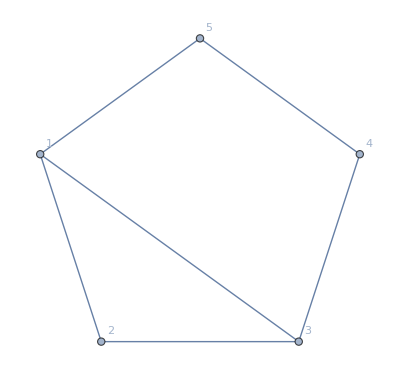

```mathematica
g= Graph[EdgeAdd[CycleGraph[5],{1<->3}],VertexLabels->"Name"]
```

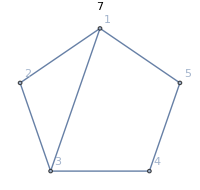
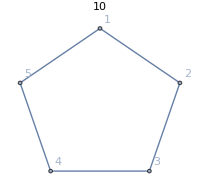
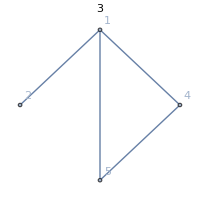
{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 7
 | 
7 | 
7 | 3
4 | 
7
2 |  | 7
 | 
7 | 2
5 | 2
5
3 |  |  | 7
 | 
7 | 3
4
4 |  |  |  | 7
 | 
7
5 |  |  |  |  | 7
}full,{{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 10
 | 
10 | 3
7 | 3
7 | 
10
2 |  | 10
 | 
10 | 3
7 | 3
7
3 |  |  | 10
 | 
10 | 3
7
4 |  |  |  | 10
 | 
10
5 |  |  |  |  | 10
}{EdgeDelete,1<->3},{-Graphics-, | 1 | 2 | 4 | 5
1 | 3
 | 
3 | 
3 | 
3
2 |  | 3
 | 1
2 | 1
2
4 |  |  | 3
 | 
3
5 |  |  |  | 3
}{EdgeContract,1<->3}}}

```mathematica
ColorMatrixForEdgeOperationMatrix[g,{1<->3},{EdgeDelete,EdgeContract}, 
Graph[#,GraphLayout->"TutteEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[#,4]/24,ImageSize->200]&]/. 0->""
```

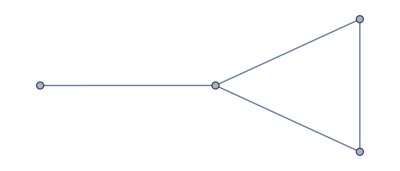

```mathematica
lollipop = Graph[{1<->2,1<->4,4<->5,5<->1}]
```

```mathematica
TableForm[GraphSolutions[lollipop,"x2==1"],TableSpacing->{0, 0}]
```

RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0]
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0]
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]

```mathematica
TableForm[GraphSolutions[Graph[plantri[[1]]],"x1==1&&x2==2"],TableSpacing->{0, 0}]
```

RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]

```mathematica
ColorMatrixForEdgeOperationMatrix[Graph[plantri[[1]]],{1<->2},{#1&}]/. 0->""
```

{{, | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 10
 | 
10 | 
10 | 
10 | 
10 | 
10 | 4
6 | 4
6 | 4
6 | 4
6 | 4
6 | 
10
2 |  | 10
 | 
10 | 4
6 | 4
6 | 
10 | 
10 | 
10 | 4
6 | 
10 | 4
6 | 4
6
3 |  |  | 10
 | 
10 | 4
6 | 4
6 | 4
6 | 
10 | 
10 | 4
6 | 
10 | 4
6
4 |  |  |  | 10
 | 
10 | 4
6 | 
10 | 4
6 | 
10 | 
10 | 4
6 | 4
6
5 |  |  |  |  | 10
 | 
10 | 4
6 | 
10 | 4
6 | 
10 | 
10 | 4
6
6 |  |  |  |  |  | 10
 | 
10 | 4
6 | 
10 | 4
6 | 
10 | 4
6
7 |  |  |  |  |  |  | 10
 | 
10 | 4
6 | 4
6 | 
10 | 
10
8 |  |  |  |  |  |  |  | 10
 | 
10 | 4
6 | 4
6 | 
10
9 |  |  |  |  |  |  |  |  | 10
 | 
10 | 4
6 | 
10
10 |  |  |  |  |  |  |  |  |  | 10
 | 
10 | 
10
11 |  |  |  |  |  |  |  |  |  |  | 10
 | 
10
12 |  |  |  |  |  |  |  |  |  |  |  | 10
}full,{{, | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 10
 | 
10 | 
10 | 
10 | 
10 | 
10 | 4
6 | 4
6 | 4
6 | 4
6 | 4
6 | 
10
2 |  | 10
 | 
10 | 4
6 | 4
6 | 
10 | 
10 | 
10 | 4
6 | 
10 | 4
6 | 4
6
3 |  |  | 10
 | 
10 | 4
6 | 4
6 | 4
6 | 
10 | 
10 | 4
6 | 
10 | 4
6
4 |  |  |  | 10
 | 
10 | 4
6 | 
10 | 4
6 | 
10 | 
10 | 4
6 | 4
6
5 |  |  |  |  | 10
 | 
10 | 4
6 | 
10 | 4
6 | 
10 | 
10 | 4
6
6 |  |  |  |  |  | 10
 | 
10 | 4
6 | 
10 | 4
6 | 
10 | 4
6
7 |  |  |  |  |  |  | 10
 | 
10 | 4
6 | 4
6 | 
10 | 
10
8 |  |  |  |  |  |  |  | 10
 | 
10 | 4
6 | 4
6 | 
10
9 |  |  |  |  |  |  |  |  | 10
 | 
10 | 4
6 | 
10
10 |  |  |  |  |  |  |  |  |  | 10
 | 
10 | 
10
11 |  |  |  |  |  |  |  |  |  |  | 10
 | 
10
12 |  |  |  |  |  |  |  |  |  |  |  | 10
}{#1&,1<->2}}}

```mathematica
PaintGraph2[VertexDelete[ Graph[plantri[[1]]],{1,2,6}],"True",GraphLayout->"TutteEmbedding", ImageSize->200, VertexSize->Large, VertexLabels->"Name"]
```

$Aborted[]